# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Solutions 06

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1.

We are given a single-step geometric binomial pricing lattice as the model for the price dynamics of a stock with current price S(0):

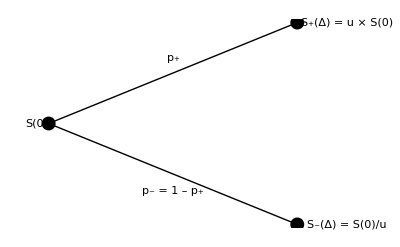

Consider a case in which S(0)  = 95, Δ = 0.25, u = 1.1, and the risk free rate of return r = 1.5%, then...

Show that the market for S(t) is arbitrage free.

What is the risk neutral measure?

What is the price at t=0 for an at-the-money put?

#### Solution

The state prices must be strictly positive:

(1
S(t))=(ⅇ^(r Δ) | ⅇ^(r Δ)
u S(t) | S(t)/u)((ψ_+)/(ψ_-))

(1
95)=(ⅇ^(0.015×0.25) | ⅇ^(0.015×0.25)
1.1×95 | 95/1.1)((ψ_+)/(ψ_-))    ⟹    ((ψ_+)/(ψ_-))=(0.494014/0.502243)>(0/0)

Thus, this market is arbitrage-free. Also note that

```mathematica
1/1.1
```

0.909091

u^-1≤ⅇ^(r Δ)≤u

0.9091≤1.0038≤1.1000

The risk neutral measure Q can be derived by normalizing the state prices

((q_+)/(q_-))=1/(ψ_++ψ_-)((ψ_+)/(ψ_-))=(0.4959/0.5041)

The price of an at-the-money put option expiring at Δ is

P(t)=ⅇ^(-r (T-t))E_Q[P(T)]=(ⅇ^(r×Δ)(max[K-u S(t),0]/max[K-S(t)/u,0]))^T((q_+)/(q_-))

P(0)=(ⅇ^(-0.015×0.25)(max[95-95×1.1,0]/max[95-95/1.1,0]))^T(0.49587/0.50413)=8.60407

## Question 2.

For an underlying whose price dynamic follows the following SDE

ⅆS(t)=μ S(t)ⅆt+σ S(t) ⅆW(t)

Let

X(t)=(S(t))^-1

Use Itô's lemma to determine the SDE which describes the price dynamics of X(t), assuming S(0)>0.

### Solution

Given the SDE

ⅆS(t) = a(S(t), t) ⅆt + b(S(t), t) ⅆW(t)

and suitably differentiable function

X(t) = g(S(t), t)

Itô's lemma states

ⅆX(t)=((∂g)/(∂S)a+(∂g)/(∂t)+1/2(∂^2 g)/(∂S^2)b^2)ⅆt+(∂g)/(∂S)bⅆW(t)

For the problem presented we have a = μ S(t), b = σ S(t), and g = 1/S(t); therefore,

(∂g)/(∂S)a=-μ/S

(∂g)/(∂t)=0

1/2(∂^2 g)/(∂S^2)b^2=σ^2/S

(∂g)/(∂S)b=-σ/S

yields

ⅆX(t)=(σ^2-μ)1/(S(t))ⅆt-σ 1/(S(t))ⅆW(t)

Finally, making the substitution (S(t))^-1→X(t) to put the expression in terms of X(t)

ⅆX(t)=(σ^2-μ)X(t)ⅆt-σ X(t)ⅆW(t)

## Question 3.

Consider a European capped-call option with strike price K, cap C, and expiration date T . With S(t) the price of the underlying and F(t) the price of the option, the capped-call gives the holder the right to exercise the option at expiry with value of a put with strike K whose value, however, is capped at a maximum pay-out C where K<C. Thus, the value at expiry can be expressed by

F(T)=min[ max[ S(T)-K, 0 ], C ]

Assume the risk free rate is r with continuous compounding. Express the value of the option at time t<T in terms of vanilla European options with appropriately chosen parameters and, if necessary, any cash position.

### Solution

An equivalent statement of the price at expiry is:

F[T]= max[S(T)-K, 0]-max[S(T)-(K+C),0]

This is easily seen if the plot of F(T) as a function of S(T) is sketched. Consider an example with K=100 and C=120

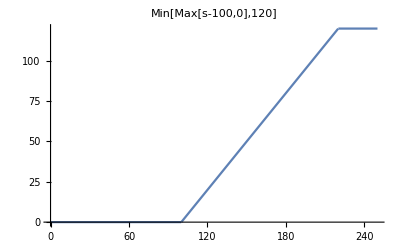

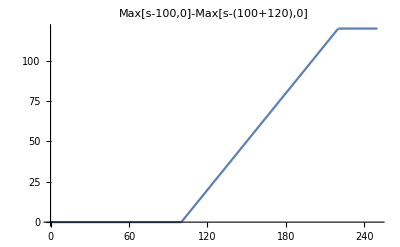

This a long position in a call with strike K and a short position in a call with strike K+C. Thus,

F(t)= C(t|K,T)-C(t|K+C,T)

## Question 4.

Consider a security priced S(t) with σ=0.22 where the risk free rate r=0.01.

Use FinancialDerivative[ ] to plot the values of a European call option for a strike K=102 and expiry T=0.5 at t=0.25 for 60≤S(t)≤140.

With the same parameters above, use FinancialDerivative[ ] to plot the values of an at-the-money European call option at t=0.25 for values of 0.1≤σ≤0.3.

### Solution

Note that the two calls to FinancialDerivative[ ] are equivalent. In the first case, where a “ReferenceTime” is given, the time to expiry is the “Expiration” less the “ReferenceTime”. In the second case, where no “ReferenceTime” is given, the “Expiration” represents the time to expiry.

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 102.00, "Expiration"->0.5},  {"InterestRate"-> 0.01, "Volatility" -> 0.22,"ReferenceTime"->0.25, "CurrentPrice"->102}]
```

4.59678

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 102.00, "Expiration"->0.25},  {"InterestRate"-> 0.01, "Volatility" -> 0.22, "CurrentPrice"->102}]
```

4.59678

The first plot shows the value of the call at for various prices of the underlying.

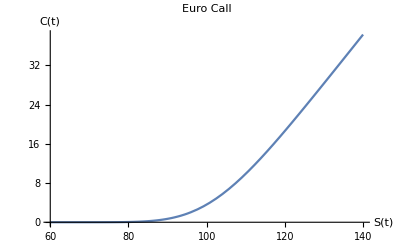

```mathematica
Plot[FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 102.00, "Expiration"->0.5},  {"InterestRate"-> 0.01, "Volatility" -> 0.22,"ReferenceTime"->0.25, "CurrentPrice"->s}],{s,60,140},PlotLabel->"Euro Call",AxesLabel->{"S(t)","C(t)"}]
```

The next plot shows the effects of varying the volatility on the option price,

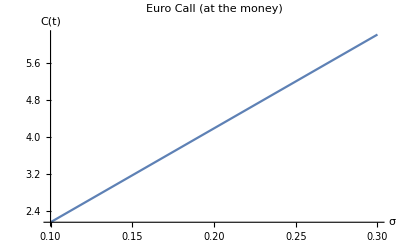

```mathematica
Plot[FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 102.00, "Expiration"->0.5},  {"InterestRate"-> 0.01, "Volatility" -> σ,"ReferenceTime"->0.25, "CurrentPrice"->102.00}],{σ,0.1,0.3},PlotLabel->"Euro Call (at the money)",AxesLabel->{"σ","C(t)"}]
```